## Appel des fonctions Mathematica

Cas de test simple linéaire:

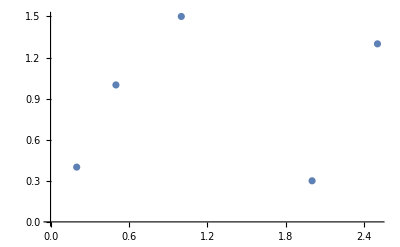

```mathematica
ListPlot[Table[Style[{{2.5,1.3},{2,0.3},{0.5,1},{1,1.5},{0.2,0.4}}]]]
```

```mathematica
Matrixlinear={{2.5,1.3}->"rond",{2,0.3}->"rond",{0.5,1}->"carre",{1,1.5}->"carre",{0.2,0.4}->"carre"};
```

### Classifiication Linéaire

```mathematica
c=Classify[Matrixlinear,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
c[{2.5,1.3},"Probabilities"]
```

<|carre→1.35999×10^-18,rond→1.|>

```mathematica
c[{1.15,0.5},"Probabilities"]
```

<|carre→0.551621,rond→0.448379|>

Regression

```mathematica
Matrixlinear2={{2.5,1.3}->1,{2,0.3}->1,{0.5,1}->0,{1,1.5}->0,{0.2,0.4}->0}; (* Mis en place de la base d'apprentissage *)
```

```mathematica
p=Predict[Matrixlinear2]
```

PredictorFunction[…]

```mathematica
(* Test sur la base d'apprentissage sortie attendue = 1 *)
```

```mathematica
p[{2.5,1.3}] 
p[{2,0.3}]
```

0.961932

1.0301

```mathematica
0.9619318204091735
```

0.961932

```mathematica
(* Test sur la base d'apprentissage sortie attendue = 0*)
```

```mathematica
p[{0.5,1}]
p[{1,1.5}]
p[{0.2,0.4}]
```

-0.0459372

0.0589405

-0.00503584

```mathematica
(* Test sur des exemple de test (inconnu pour le modèle) sortie attendue = 1*)
```

```mathematica
p[{2.22,1.6}] 
p[{1.5,0.1}]
```

0.702466

0.821395

```mathematica
(* Test sur des exemple de test (inconnu pour le modèle) sortie attendue = 0*)
```

```mathematica
p[{0.2,0.2}]
p[{0.6,1.3}]
p[{0.5,0.2}]
```

0.0641828

-0.0941803

0.230937

#### Cas de Test simple linéaire

```mathematica
Clear[a,b,c,positivePointsL, negativePointsL, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
f[3]
```

-7/4

```mathematica
3 - (-a/b*3+c/b)
```

19/4

```mathematica
positivePointsL = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0, 10}]}, {i,1, 15}]
```

{{1.63357,7.03613},{4.45762,4.76066},{-4.14846,14.6576},{-4.58898,6.89322},{-2.63792,8.0913},{-1.42283,7.28167},{-2.45487,4.20914},{-3.94033,12.7102},{-1.70762,12.8197},{-2.15557,12.9167},{-0.860039,3.57065},{-2.18121,5.60246},{-4.74362,11.1364},{-3.72633,10.6984},{-0.246605,3.77077}}

```mathematica
negativePointsL = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0, 10 }]}, {i,1,15}]
```

{{3.93539,-6.48689},{-2.36548,2.64369},{1.8262,-8.89017},{2.35111,-6.80924},{-0.10379,-7.36387},{0.372966,-4.05126},{-0.645909,-3.99446},{4.99552,-7.25393},{-4.42409,3.70909},{0.284125,-1.89135},{2.15665,-1.35134},{-1.24458,-3.27328},{3.30519,-4.34259},{1.75614,-1.23517},{-3.22197,-0.563381}}

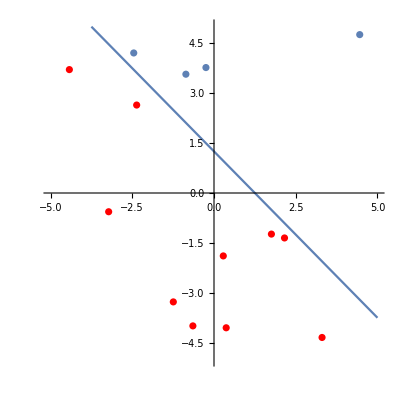

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePointsL, PlotStyle->Red],
ListPlot[positivePointsL]]
```

```mathematica
X=FlattenAt[{positivePointsL, negativePointsL},{{1},{2}}]
Y = {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1, -1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1};
```

{{1.63357,7.03613},{4.45762,4.76066},{-4.14846,14.6576},{-4.58898,6.89322},{-2.63792,8.0913},{-1.42283,7.28167},{-2.45487,4.20914},{-3.94033,12.7102},{-1.70762,12.8197},{-2.15557,12.9167},{-0.860039,3.57065},{-2.18121,5.60246},{-4.74362,11.1364},{-3.72633,10.6984},{-0.246605,3.77077},{3.93539,-6.48689},{-2.36548,2.64369},{1.8262,-8.89017},{2.35111,-6.80924},{-0.10379,-7.36387},{0.372966,-4.05126},{-0.645909,-3.99446},{4.99552,-7.25393},{-4.42409,3.70909},{0.284125,-1.89135},{2.15665,-1.35134},{-1.24458,-3.27328},{3.30519,-4.34259},{1.75614,-1.23517},{-3.22197,-0.563381}}

```mathematica
Length[X]
```

30

```mathematica
Xtest = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
transform[x_] := If[x < 0, -1, 1]
```

```mathematica
valuesXtest =Table[Xtest[[i]][[2]] - (-a/b*Xtest[[i]][[1]]+c/b),{i, Length[Xtest]}];
```

```mathematica
Length[valuesXtest]
```

2601

```mathematica
expectedOutputs = transform /@ valuesXtest;
```

#### Classification

```mathematica
ClassSimpl=Classify[X->Y,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[ClassSimpl, Xtest-> expectedOutputs, "Accuracy"]
```

0.886198

```mathematica
ClassSimpl[{2.5,1.3}]
```

1

```mathematica
positive = Select[Xtest,ClassSimpl[#]== 1&]; 
negative =Select[Xtest,ClassSimpl[#]== -1&];
```

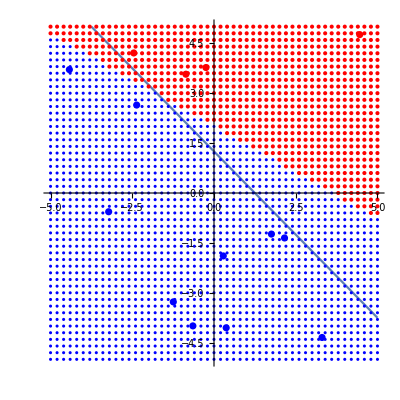

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

```mathematica
(* avec plus d'element en Red et Blue, le classify trouve plus  precisement la separation *)
```

#### RBF

```mathematica
RBF=Classify[X->Y,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[RBF, Xtest-> expectedOutputs, "Accuracy"]
```

0.699346

```mathematica
positive = Select[XLineartest2,RBF[#]== 1&]; 
negative =Select[XLineartest2,RBF[#]== -1&];
```

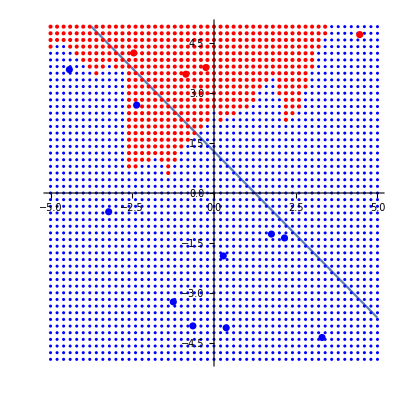

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

```mathematica
RBF[{2.5,1.3}]
```

-1

#### Reseaux neuronal

```mathematica
NN=Classify[X->Y,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
NN[{2.5,1.3}]
```

1

```mathematica
ClassifierMeasurements[NN, Xtest-> expectedOutputs, "Accuracy"]
```

0.922722

```mathematica
positive = Select[XLineartest2,NN[#]== 1&]; 
negative =Select[XLineartest2,NN[#]== -1&];
```

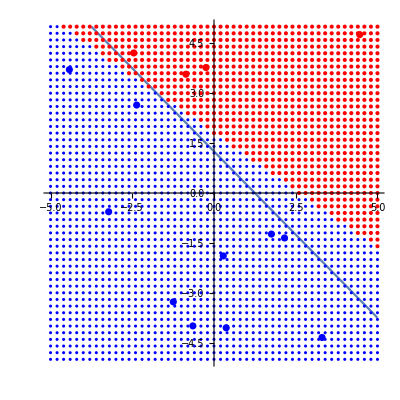

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

#### Support Vecteur Machine

```mathematica
SVM=Classify[X->Y,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
SVM[{2.5,1.3}]
```

-1

```mathematica
ClassifierMeasurements[ClassSimpl, Xtest-> expectedOutputs, "Accuracy"]
```

0.886198

```mathematica
positive = Select[XLineartest2,SVM[#]== 1&]; 
negative =Select[XLineartest2,SVM[#]== -1&];
```

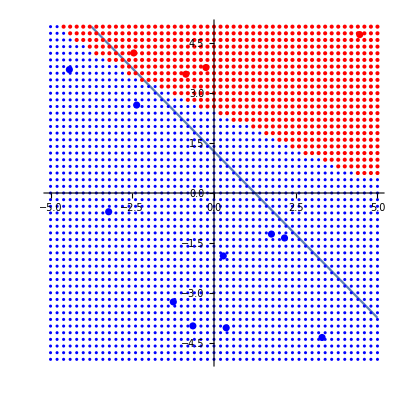

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

Simple Non Linéairement Séparable

```mathematica
Clear[redPointsNL, bluePointsNL];
```

```mathematica
g[x_] :=a*Power[x,2]
```

```mathematica
g[3]
```

36

```mathematica
bluePointsNL =  Table[x= RandomReal[{-5, 5}]; {x, g[x] + RandomReal[{0, 10}]}, {i,1, 15}]
redPointsNL = Table[x = RandomReal[{-5, 5}];
{x, g[x]-RandomReal[{0, 10 }]}, {i,1,15}]
```

{{3.46334,49.109},{-2.4636,29.9609},{-2.46799,32.9495},{-3.6747,60.4588},{3.03608,43.3547},{-0.443405,6.62952},{-3.10806,41.2087},{2.28371,26.7271},{-0.96256,4.90661},{4.03773,72.7099},{2.75483,31.1457},{3.48815,52.8207},{0.612027,3.29343},{-4.62169,91.1064},{4.99652,107.962}}

{{-1.50779,0.248516},{1.10751,3.24593},{-1.57885,0.652655},{2.87911,24.0329},{-1.76031,4.61081},{-1.69816,5.02876},{3.25004,40.6289},{-1.68144,6.77038},{-3.03196,30.5144},{-3.38546,36.6411},{-3.53378,44.8112},{-4.59981,78.3384},{-0.0127858,-1.86849},{1.15712,0.745953},{-4.96237,96.6733}}

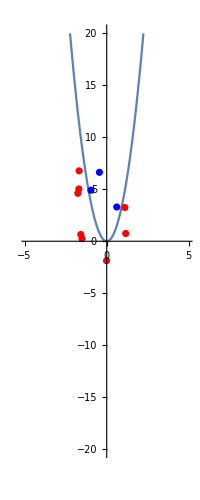

```mathematica
Show[Plot[g[x], {x,-20, 20}, PlotRange->{-20,20},
AspectRatio->1],
ListPlot[redPointsNL, PlotStyle->Red,AspectRatio->Full,PlotRange->{-20,20}],
ListPlot[bluePointsNL, PlotStyle->Blue],AspectRatio->Full,PlotRange->{-20,20}]
```

```mathematica
(* voici une vue des sur laquel nous allons nous baser pour les test non lineairement separable *)
```

```mathematica
X=FlattenAt[{redPointsNL, bluePointsNL},{{1},{2}}]
Y = Flatten[{Table[1, Length[redPointsNL]], Table[-1, Length[bluePointsNL]]}]
```

{{-1.50779,0.248516},{1.10751,3.24593},{-1.57885,0.652655},{2.87911,24.0329},{-1.76031,4.61081},{-1.69816,5.02876},{3.25004,40.6289},{-1.68144,6.77038},{-3.03196,30.5144},{-3.38546,36.6411},{-3.53378,44.8112},{-4.59981,78.3384},{-0.0127858,-1.86849},{1.15712,0.745953},{-4.96237,96.6733},{3.46334,49.109},{-2.4636,29.9609},{-2.46799,32.9495},{-3.6747,60.4588},{3.03608,43.3547},{-0.443405,6.62952},{-3.10806,41.2087},{2.28371,26.7271},{-0.96256,4.90661},{4.03773,72.7099},{2.75483,31.1457},{3.48815,52.8207},{0.612027,3.29343},{-4.62169,91.1064},{4.99652,107.962}}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Length[X]
```

30

```mathematica
Xunlineartest = Partition[Flatten[Table[{i,j},{i, -10, 10, 0.5}, {j, -10, 10, 0.5}]], 2];
```

```mathematica
valuesXtest2 =Table[Xunlineartest[[i]][[2]] - (a*Power[Xunlineartest[[i]][[1]],2]),{i, Length[Xunlineartest]}];
```

```mathematica
expectedOutputs2 = transform /@ valuesXtest2;
```

#### Classification

```mathematica
ClassSimpl2=Classify[X->Y,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassSimpl2[{2.5,1.3}]
```

1

```mathematica
ClassifierMeasurements[ClassSimpl2, Xunlineartest-> expectedOutputs2, "Accuracy"]
```

0.425342

```mathematica
positive2 = Select[Xunlineartest,ClassSimpl2[#]== 1&]; 
negative2 =Select[Xunlineartest,ClassSimpl2[#]== -1&];
```

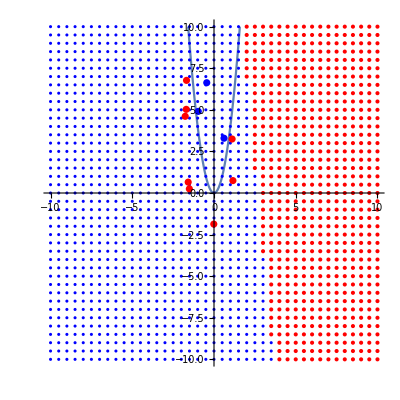

```mathematica
Show[Plot[g[x], {x,-10, 10}, PlotRange->{-10,10},
AspectRatio->1],ListPlot[positive2, PlotStyle->Blue], ListPlot[negative2, PlotStyle->Red], ListPlot[bluePointsNL, PlotStyle->Blue, PlotStyle->Thick, PlotRange->{-10,10},AspectRatio->1],
ListPlot[redPointsNL, PlotStyle->Red, PlotStyle->Thick,PlotRange->{-10,10},AspectRatio->1]]
```

#### RBF

```mathematica
RBF2=Classify[X->Y,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[RBF2, Xunlineartest-> expectedOutputs2, "Accuracy"]
```

0.221297

```mathematica
positive2 = Select[Xunlineartest,RBF2[#]== 1&]; 
negative2 =Select[Xunlineartest,RBF2[#]== -1&];
```

```mathematica
RBF2[{2.5,1.3}]
```

1

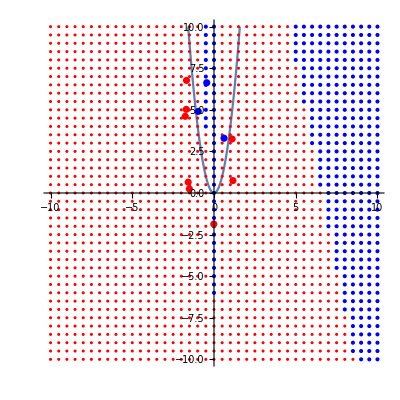

```mathematica
Show[Plot[g[x], {x,-10, 10}, PlotRange->{-10,10},
AspectRatio->1],ListPlot[positive2, PlotStyle->Red], ListPlot[negative2, PlotStyle->Blue], ListPlot[bluePointsNL, PlotStyle->Blue, PlotStyle->Thick, PlotRange->{-10,10},AspectRatio->Full],
ListPlot[redPointsNL, PlotStyle->Red, PlotStyle->Thick,PlotRange->{-10,10},AspectRatio->Full]]
```

#### Reseaux neuronal

```mathematica
NN2=Classify[X->Y,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
NN2[{2.5,1.3}]
```

1

```mathematica
ClassifierMeasurements[NN2, Xunlineartest-> expectedOutputs2, "Accuracy"]
```

0.0232005

```mathematica
positive2 = Select[Xunlineartest,NN2[#]== 1&]; 
negative2 =Select[Xunlineartest,NN2[#]== -1&];
```

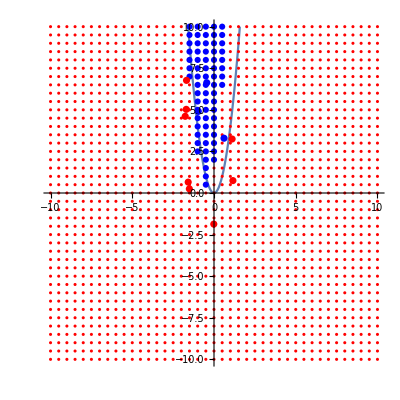

```mathematica
Show[Plot[g[x], {x,-10, 10}, PlotRange->{-10,10},
AspectRatio->1],ListPlot[positive2, PlotStyle->Red], ListPlot[negative2, PlotStyle->Blue], ListPlot[bluePointsNL, PlotStyle->Blue, PlotStyle->Thick, PlotRange->{-10,10},AspectRatio->Full],
ListPlot[redPointsNL, PlotStyle->Red, PlotStyle->Thick,PlotRange->{-10,10},AspectRatio->Full]]
```

#### Support Vecteur Machine

```mathematica
SVM2=Classify[X->Y,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
SVM2[{2.5,1.3}]
```

1

```mathematica
ClassifierMeasurements[SVM2, Xunlineartest-> expectedOutputs2, "Accuracy"]
```

0.0220107

```mathematica
positive2 = Select[Xunlineartest,SVM2[#]== 1&]; 
negative2 =Select[Xunlineartest,SVM2[#]== -1&];
```

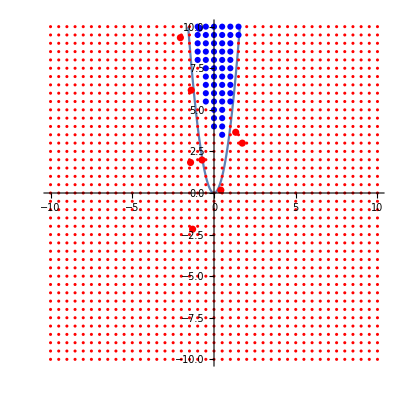

```mathematica
Show[Plot[g[x], {x,-10, 10}, PlotRange->{-10,10},
AspectRatio->1],ListPlot[positive2, PlotStyle->Red], ListPlot[negative2, PlotStyle->Blue], ListPlot[bluePointsNL, PlotStyle->Blue, PlotStyle->Thick, PlotRange->{-10,10},AspectRatio->Full],
ListPlot[redPointsNL, PlotStyle->Red, PlotStyle->Thick,PlotRange->{-10,10},AspectRatio->Full]]
```

Cross